# Sum-of-squares certificates for every θ: algebraic verification

Partially entangled Tsirelson family: state cosθ|00⟩ + sinθ|11⟩, settings a0 = π/4, a1 = -π/4, b0 = 0, b1 = π/2. For each vertex V of the local polygon, the vertex Bell expression β (normalised to value 1 on the optimal realisation) has an SOS certificate valid for all θ in its range (SOS theorem of App. C).

With v ∈ (0,1] defined by tanθ = (√2 - 1) + (2 - √2) v, i.e. θ ∈ (π/8, π/4], each certificate consists of nullifiers N_a(v), a symmetric polynomial matrix W(v) and a scalar μ(v) such that

    μ(v) (Id - β) = ∑_ab W_ab(v) aj[N_a] ** N_b ,

with W(v) positive definite and μ(v) > 0 on the range. This notebook checks, in exact arithmetic: (0) the vertex Bell expressions β are the Bell expression derived in Orthogonal.nb, evaluated at the vertices; (1) the N_a annihilate the optimal state and vanish on the two saturated deterministic behaviours; (2) the identity holds as an identity of noncommutative polynomials modulo A_x.b2 = B_y.b2 = Id and [A_x, B_y] = 0; (3) W(v) > 0 and μ(v) > 0 on the range (cylindrical algebraic decomposition on the leading principal minors).

## NCAlgebra package

```mathematica
<< NCAlgebra`
```

```mathematica
SetCommutative[v, rr, a0, a1, b0, b1];
SetNonCommutative[A0, A1, B0, B1];

myRules = {
   A0 ** A0 -> Id,
   A1 ** A1 -> Id,
   B0 ** B0 -> Id,
   B1 ** B1 -> Id,
   B0 ** A0 -> A0 ** B0,
   B0 ** A1 -> A1 ** B0,
   B1 ** A0 -> A0 ** B1,
   B1 ** A1 -> A1 ** B1
   };

aj[A0] := A0;
aj[A1] := A1;
aj[B0] := B0;
aj[B1] := B1;
v /: Conjugate[v] = v;
```

As in the θ = π/4 notebook, NCQuadraticForm[vec1, mat, vec2] returns ∑_ij aj[vec1_i] ** mat_ij ** vec2_j reduced with myRules. Here each product aj[vec1_i] ** vec2_j is reduced first and then combined with the scalar entries mat_ij, which is equivalent and much faster.

```mathematica
NCQuadraticForm[vec1_List, mat_List, vec2_List] := 
  Expand[Sum[mat[[i, j]] NCExpandReplaceRepeated[aj[vec1[[i]]] ** vec2[[j]], myRules], {i, Length[vec1]}, {j, Length[vec2]}]];
```

## Helper functions

Operators of the qubit realisation (as in the θ = π/4 notebook) and the state |00⟩ + tanθ |11⟩ (normalisation is irrelevant):

```mathematica
X = PauliMatrix[1]; Z = PauliMatrix[3]; I2 = IdentityMatrix[2];
ZA = KroneckerProduct[Z, I2]; XA = KroneckerProduct[X, I2];
ZB = KroneckerProduct[I2, Z]; XB = KroneckerProduct[I2, X];
II = IdentityMatrix[4];
A[i_] := (ZA + (-1)^i XA)/Sqrt[2];
B[0] = ZB;
B[1] = XB;
psi[v_] := {1, 0, 0, (Sqrt[2] - 1) + (2 - Sqrt[2]) v};
```

toMatrix turns a noncommutative polynomial into the corresponding 4×4 operator; atDeterministic evaluates it on a deterministic behaviour (A0, A1, B0, B1) ∈ {±1}^4; zeroQ decides exactly whether a polynomial in v, the monomials and √2 is zero; leadingMinors returns the leading principal minors as polynomials in v.

```mathematica
toMatrix[expr_] := Module[{e = NCExpand[expr], c0},
   c0 = e /. {A0 -> 0, A1 -> 0, B0 -> 0, B1 -> 0};
   c0 II + ((e - c0) /. NonCommutativeMultiply -> Dot /. {A0 -> A[0], A1 -> A[1], B0 -> B[0], B1 -> B[1]})];

atDeterministic[expr_, {a0v_, a1v_, b0v_, b1v_}] := 
  NCExpand[expr] /. NonCommutativeMultiply -> Times /. {A0 -> a0v, A1 -> a1v, B0 -> b0v, B1 -> b1v, Id -> 1};

zeroQ[e_] := Module[{monos, com},
   monos = DeleteDuplicates[Cases[e, _NonCommutativeMultiply, {0, Infinity}]];
   com = e /. Thread[monos -> Array[mm, Length[monos]]] /. {A0 -> a0, A1 -> a1, B0 -> b0, B1 -> b1};
   com = Expand[com /. {Power[2, 1/2] -> rr, Power[2, -1/2] -> rr/2}];
   Expand[PolynomialRemainder[com, rr^2 - 2, rr]] === 0];

leadingMinors[W_] := Module[{Wr = W /. {Power[2, 1/2] -> rr, Power[2, -1/2] -> rr/2}},
   Table[Expand[PolynomialRemainder[Expand[Det[Wr[[;; k, ;; k]]]], rr^2 - 2, rr]] /. rr -> Sqrt[2], {k, Length[W]}]];
```

## Data

The certificates are stored in UniformSOS_data.wl. The next cell loads it from the directory of this notebook, so keep the two files together. vbar is the value of v at θbar, where the hexagon becomes an octagon.

```mathematica
SetDirectory[NotebookDirectory[]];
Get["UniformSOS_data.wl"];
Keys[certs]
```

{V1,V2,V3,V4,V5,V6}

```mathematica
theta[v_] := ArcTan[(Sqrt[2] - 1) + (2 - Sqrt[2]) v];
{N[vbar, 12], N[theta[0], 12], N[theta[vbar], 12], N[theta[1], 12]}
```

{0.575995310581,0.392699081699,0.644539533252,0.785398163397}

## Bell expressions: from Orthogonal.nb to the vertices

The plane of Bell expressions is derived in Orthogonal.nb, section SOS Decomposition, cell Collect[FullSimplify[Transpose[β] . M], {p[1], p[4]}]. Its output is pasted below. To check it, evaluate that cell in Orthogonal.nb, copy the output and paste it in place of the argument of fromOrthogonal. There A[x], B[y] are commuting symbols and A[x] . B[y] are their products. fromOrthogonal hides the 4×4 matrices A[i], B[y] defined above, so that the pasted expression is not turned into matrices, and rewrites it with the noncommutative variables A0, A1, B0, B1. coeffs returns the coefficients of a Bell expression in the order (Id, A0, A1, B0, B1, A0B0, A0B1, A1B0, A1B1).

```mathematica
SetAttributes[fromOrthogonal, HoldAll];
fromOrthogonal[expr_] := Block[{A, B}, Module[{rules = {A[0] -> A0, A[1] -> A1, B[0] -> B0, B[1] -> B1}},
    expr /. Dot[x_, y_] :> NonCommutativeMultiply[x /. rules, y /. rules] /. rules]];

corrBasis = {A0, A1, B0, B1, A0 ** B0, A0 ** B1, A1 ** B0, A1 ** B1};
coeffs[e_] := Module[{syms = {A0, A1, B0, B1, ab00, ab01, ab10, ab11}, ee},
   ee = Expand[NCExpand[e] /. Thread[corrBasis[[5 ;;]] -> syms[[5 ;;]]]];
   Prepend[Coefficient[ee, syms], ee /. Thread[syms -> 0] /. Id -> 1]];
```

```mathematica
betaOrth = fromOrthogonal[
   -((1/(2*(3 - Cos[4*θ])))*(p[4]*(-4*B[1]*(-3 + Cos[4*θ]) + Sqrt[2]*(-5*Cos[2*θ] + Cos[6*θ])*A[0] . B[1] + Sqrt[2]*(-5*Cos[2*θ] + Cos[6*θ])*A[1] . B[1] + 2*Sqrt[2]*A[0]*(-3 + Cos[4*θ])*Sin[2*θ] - 2*Sqrt[2]*A[1]*(-3 + Cos[4*θ])*Sin[2*θ]))) - (-4*B[0]*Cos[2*θ] - Sqrt[2]*A[0] . B[0] + Sqrt[2]*Cos[4*θ]*A[0] . B[0] - Sqrt[2]*A[1] . B[0] + Sqrt[2]*Cos[4*θ]*A[1] . B[0] - 2*Sqrt[2]*A[0] . B[1]*Sin[2*θ] + 2*Sqrt[2]*A[1] . B[1]*Sin[2*θ])/(2*(3 - Cos[4*θ])) - (1/(2*(3 - Cos[4*θ])))*(p[1]*(Sqrt[2]*A[0]*(-3 + Cos[4*θ]) + Sqrt[2]*A[1]*(-3 + Cos[4*θ]) - 4*B[0]*(-1 + Cos[4*θ]) + 2*Sqrt[2]*Cos[2*θ]*A[0] . B[0] + 2*Sqrt[2]*Cos[2*θ]*A[1] . B[0] - 2*Sqrt[2]*Cos[2*θ]*A[0] . B[1]*Sin[2*θ] + Sqrt[2]*A[1] . B[1]*Sin[4*θ]))
   ];
```

The coordinates of the paper are r0 = p[1] and r1 = 2 p[4]. With tanθ = (√2 - 1) + (2 - √2) v, every trigonometric function of 2θ, 4θ, 6θ becomes a rational function of v:

```mathematica
tv = (Sqrt[2] - 1) + (2 - Sqrt[2]) v;
toV[e_] := Together[TrigExpand[e] /. {Cos[θ] -> 1/Sqrt[1 + tv^2], Sin[θ] -> tv/Sqrt[1 + tv^2]}];
betaV = Simplify[toV[coeffs[betaOrth]] /. {p[1] -> r0, p[4] -> r1/2}];
TableForm[Collect[betaV, {r0, r1}, Factor], TableHeadings -> {{"Id", "A0", "A1", "B0", "B1", "A0B0", "A0B1", "A1B0", "A1B1"}, None}]
```

Id | 0
A0 | -(r1 (2-√2-2 v+2 √2 v))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2))-(r0 (-2+2 √2+6 v-4 √2 v-4 v^2+3 √2 v^2))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2))
A1 | (r1 (2-√2-2 v+2 √2 v))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2))-(r0 (-2+2 √2+6 v-4 √2 v-4 v^2+3 √2 v^2))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2))
B0 | -(2 r0 (-3+2 √2+8 v-6 √2 v-6 v^2+4 √2 v^2))/(-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4)-((-1+v) (4-3 √2-20 v+14 √2 v+31 v^2-22 √2 v^2-17 v^3+12 √2 v^3))/(-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4)
B1 | -r1
A0B0 | -(-4+3 √2+12 v-8 √2 v-8 v^2+6 √2 v^2)/(2 (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))-(r0 (-1+v) (6-4 √2-28 v+20 √2 v+44 v^2-31 √2 v^2-24 v^3+17 √2 v^3))/(2 (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))
A0B1 | -(r0 (-1+v) (-14+10 √2+88 v-62 √2 v-202 v^2+143 √2 v^2+208 v^3-147 √2 v^3-82 v^4+58 √2 v^4))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))+(20-14 √2-124 v+88 √2 v+320 v^2-226 √2 v^2-424 v^3+300 √2 v^3+290 v^4-205 √2 v^4-82 v^5+58 √2 v^5)/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))-(r1 (-1+v) (30-21 √2-196 v+139 √2 v+504 v^2-356 √2 v^2-656 v^3+464 √2 v^3+454 v^4-321 √2 v^4-140 v^5+99 √2 v^5))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))
A1B0 | -(-4+3 √2+12 v-8 √2 v-8 v^2+6 √2 v^2)/(2 (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))-(r0 (-1+v) (6-4 √2-28 v+20 √2 v+44 v^2-31 √2 v^2-24 v^3+17 √2 v^3))/(2 (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))
A1B1 | (r0 (-1+v) (-14+10 √2+88 v-62 √2 v-202 v^2+143 √2 v^2+208 v^3-147 √2 v^3-82 v^4+58 √2 v^4))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))-(20-14 √2-124 v+88 √2 v+320 v^2-226 √2 v^2-424 v^3+300 √2 v^3+290 v^4-205 √2 v^4-82 v^5+58 √2 v^5)/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))-(r1 (-1+v) (30-21 √2-196 v+139 √2 v+504 v^2-356 √2 v^2-656 v^3+464 √2 v^3+454 v^4-321 √2 v^4-140 v^5+99 √2 v^5))/(2 (-2+√2+4 v-3 √2 v-3 v^2+2 √2 v^2) (-9+6 √2+36 v-26 √2 v-60 v^2+42 √2 v^2+48 v^3-34 √2 v^3-17 v^4+12 √2 v^4))

This is the plane β^(0) + r0 β^(1) + r1 β^(2) of the paper (App. C), with c = cos2θ = (1 - tanθ^2)/(1 + tanθ^2) and s = sin2θ = 2 tanθ/(1 + tanθ^2):

```mathematica
paperPlane = Module[{cth = (1 - tv^2)/(1 + tv^2), sth = 2 tv/(1 + tv^2), kk},
   kk = 1 + sth^2;
   {0, 0, 0, cth/kk, 0, sth^2/(Sqrt[2] kk), sth/(Sqrt[2] kk), sth^2/(Sqrt[2] kk), -sth/(Sqrt[2] kk)} +
   r0 {0, 1/Sqrt[2], 1/Sqrt[2], -2 sth^2/kk, 0, -cth/(Sqrt[2] kk), sth cth/(Sqrt[2] kk), -cth/(Sqrt[2] kk), -sth cth/(Sqrt[2] kk)} +
   r1 {0, sth/Sqrt[2], -sth/Sqrt[2], 0, -1, 0, cth/Sqrt[2], 0, cth/Sqrt[2]}];
Simplify[betaV - paperPlane]
```

{0,0,0,0,0,0,0,0,0}

Each family is the intersection of the lines β·D = 1 of its two saturated deterministic behaviours D, stored in certs[name]["deterministic"] as (A0, A1, B0, B1). Solving these two linear equations gives the vertex (r0(v), r1(v)) exactly. The table shows it at the middle of each range:

```mathematica
detVec[{x0_, x1_, y0_, y1_}] := {0, x0, x1, y0, y1, x0 y0, x0 y1, x1 y0, x1 y1};
vertex[name_] := Simplify[First[Solve[Table[betaV . detVec[d] == 1, {d, certs[name]["deterministic"]}], {r0, r1}]]];
TableForm[Table[Module[{vm = Mean[certs[name]["range"]]},
   {name, certs[name]["vertex"], N[vm, 6], N[{r0, r1} /. vertex[name] /. v -> vm, 6]}], {name, Keys[certs]}],
 TableHeadings -> {None, {"family", "lines", "v", "(r0, r1)"}}]
```

family | lines | v | (r0, r1)
V1 | II(+1,+1) & II(-1,+1) | 0.5 | -0.166667
0
V2 | I(+1,+1) & II(-1,+1) | 0.287998 | 0.101641
-0.311223
V3 | I(+1,+1) & II(-1,-1) | 0.5 | 0.358208
-0.147501
V4 | II(+1,-1) & II(-1,-1) | 0.5 | 0.4
0
V5 | II(-1,+1) & I(-1,+1) | 0.787998 | -0.141923
-0.246291
V6 | I(+1,+1) & I(-1,+1) | 0.787998 | -0.0264685
-0.296603

At these points no deterministic behaviour gives more than 1. Here this is checked at three values of v inside each range. The proof for every v is polygon_proof.wl.

```mathematica
allDet = Tuples[{-1, 1}, 4];
Table[Module[{lo, hi},
   {lo, hi} = certs[name]["range"];
   {name, Table[N[Max[N[(betaV /. vertex[name]) . detVec[#] & /@ allDet /. v -> lo + x (hi - lo), 30]], 10], {x, {1/4, 1/2, 3/4}}]}],
  {name, Keys[certs]}] // TableForm
```

V1 | 1.
1.
1.
V2 | 1.
1.
1.
V3 | 1.
1.
1.
V4 | 1.
1.
1.
V5 | 1.
1.
1.
V6 | 1.
1.
1.

The Bell expression of Orthogonal.nb at each vertex is exactly the β of the certificates in UniformSOS_data.wl:

```mathematica
bellCheck = Table[{name, Simplify[(betaV /. vertex[name]) - coeffs[certs[name]["beta"]]]}, {name, Keys[certs]}];
TableForm[bellCheck]
```

V1 | 0
0
0
0
0
0
0
0
0
V2 | 0
0
0
0
0
0
0
0
0
V3 | 0
0
0
0
0
0
0
0
0
V4 | 0
0
0
0
0
0
0
0
0
V5 | 0
0
0
0
0
0
0
0
0
V6 | 0
0
0
0
0
0
0
0
0

```mathematica
AllTrue[Flatten[bellCheck[[All, 2]]], # === 0 &]
```

True

## One vertex in detail: V1 = II(+1,+1) ∩ II(-1,+1)

```mathematica
c = certs["V1"];
{c["vertex"], c["level"], c["range"], c["deterministic"]}
```

{II(+1,+1) & II(-1,+1),1+A+B+BB'+AB+ABB',{0,1},{{1,-1,1,1},{-1,1,1,-1}}}

### Bell expression

```mathematica
beta = c["beta"];
Collect[beta, {A0, A1, B0, B1, A0 ** B0, A0 ** B1, A1 ** B0, A1 ** B1}, Simplify]
```

(B0 (2+√2-v) v)/(1+(2+3 √2) v+v^2)+(A0 (1-4 v+(3-2 √2) v^2+(-2+√2) v^3))/(2 (1+(2+3 √2) v+v^2))+(A1 (1-4 v+(3-2 √2) v^2+(-2+√2) v^3))/(2 (1+(2+3 √2) v+v^2))+((-1+√2) (2+√2-v) v (2+3 √2+2 v) A0**B0)/(2 √2 (1+(2+3 √2) v+v^2))+((1/(√2)+v)^2 A0**B1)/(1+(2+3 √2) v+v^2)+((-1+√2) (2+√2-v) v (2+3 √2+2 v) A1**B0)/(2 √2 (1+(2+3 √2) v+v^2))-((√2+2 v)^2 A1**B1)/(4 (1+(2+3 √2) v+v^2))

At v = 1 (θ = π/4) this is the octagon vertex (r0, r1) = (-(1 - 1/√2), 0) of Barizien and Bancal, β = CHSH/(2√2) - (1 - 1/√2)((A0 + A1)/√2 - B0):

```mathematica
zeroQ[(beta /. v -> 1) - ((A0 ** B0 + A0 ** B1 + A1 ** B0 - A1 ** B1)/(2 Sqrt[2]) - (1 - 1/Sqrt[2]) ((A0 + A1)/Sqrt[2] - B0))]
```

True

### Nullifiers

```mathematica
NN = c["nullifiers"];
NN // MatrixForm
```

(1+A0/(√2)+A1/(√2)-B0-(A0**B0)/(√2)-(A1**B0)/(√2)
√2 A0**B1+√2 A1**B1+B0**B1-B1**B0
A0+A1-√2 B0+(A0**B0**B1)/(√2)+(A0**B1**B0)/(√2)
B1-(B0**B1)/2-(B1**B0)/2+(A0**B0**B1)/(√2)+(A1**B0**B1)/(√2)
A0+A1-√2 B0+B1-(B0**B1)/2-(B1**B0)/2+(A0**B0**B1)/(√2)-(A1**B1**B0)/(√2)
1/(√2)+(-1-1/(√2)) B1+B0 (2+3/(√2)-v)+v+A0 (-1-√2+√2 v)+A1 (-1-√2+√2 v)+(-1-√2) A0**B1+(1+1/(√2)) B1**B0+(-1-√2) A0**B0**B1
1+√2 A0-B0+B1 (1-√2-2 v+√2 v)-√2 A0**B0+(-1+√2+2 v-√2 v) B0**B1
1-√2 A1+B0+A0 (-1+√2+2 v-√2 v)+B1 (1-2 √2-2 v+√2 v)+(-1+2 v-√2 v) A0**B0-A0**B1+(1-2 v+√2 v) B1**B0-A0**B0**B1
1+A0/(√2)-B0-(A0**B0)/(√2)+(-1+1/(√2)+v-√2 v) A0**B1+(1-1/(√2)-v+√2 v) A0**B0**B1)

They annihilate the optimal state for every v ...

```mathematica
Table[Simplify[toMatrix[NN[[i]]] . psi[v]], {i, Length[NN]}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

... and vanish on the two saturated deterministic behaviours:

```mathematica
Table[Simplify[atDeterministic[NN[[i]], d]], {i, Length[NN]}, {d, c["deterministic"]}]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

### Gram matrix and prefactor

```mathematica
W = c["W"]; mu = c["mu"];
{Dimensions[W], Exponent[W[[1, 1]], v], mu}
```

{{9,9},3,(4+4 √2) (1+(2+3 √2) v+v^2)}

```mathematica
W[[1, 1]]
```

-1490212589607/2500+(263434857276 √2)/625+(1857932377021 v)/1250-(2627513149853 v)/(1250 √2)-(404140032 v^2)/125+(285769728 √2 v^2)/125-(659977216 v^3)/625+(466673664 √2 v^3)/625

```mathematica
N[W /. v -> 1/2, 4] // MatrixForm
```

(3.925 | 0.2957 | -0.6059 | 0.1963 | 0.9043 | 0.3641 | -2.234 | 0.09421 | -0.6582
0.2957 | 1.478 | -1.004 | 0.9992 | 1.199 | 0.1328 | -0.5379 | 0.8307 | 0.3912
-0.6059 | -1.004 | 2.476 | 0 | -1.829 | 0.1941 | 1.123 | -0.3041 | -1.058
0.1963 | 0.9992 | 0 | 2.481 | 0.6123 | 0.6012 | 0.9935 | 0.6423 | -1.805
0.9043 | 1.199 | -1.829 | 0.6123 | 2.626 | 0.1314 | -0.9129 | 0.558 | -0.2424
0.3641 | 0.1328 | 0.1941 | 0.6012 | 0.1314 | 0.8799 | 0.7966 | -0.9371 | -0.3133
-2.234 | -0.5379 | 1.123 | 0.9935 | -0.9129 | 0.7966 | 3.977 | -1.419 | -1.55
0.09421 | 0.8307 | -0.3041 | 0.6423 | 0.558 | -0.9371 | -1.419 | 2.442 | -0.451
-0.6582 | 0.3912 | -1.058 | -1.805 | -0.2424 | -0.3133 | -1.55 | -0.451 | 5.422)

### The identity

μ(v)(Id - β) - ∑_ab W_ab aj[N_a] ** N_b reduces to zero:

```mathematica
lhs = NCQuadraticForm[NN, W, NN];
rhs = NCExpandReplaceRepeated[mu (Id - beta), myRules];
zeroQ[lhs - rhs]
```

True

### Positivity

All leading principal minors of W(v) are positive for 0 < v ≤ 1, and μ(v) > 0:

```mathematica
minors = leadingMinors[W];
Exponent[#, v] & /@ minors
```

{3,6,9,12,15,18,21,24,27}

```mathematica
Resolve[ForAll[v, 0 < v <= 1, And @@ Thread[minors > 0] && mu > 0], Reals]
```

True

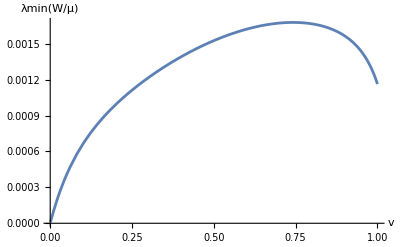

```mathematica
Plot[Min[Eigenvalues[N[W/mu /. v -> x]]], {x, 0.001, 1}, AxesLabel -> {"v", "λmin(W/μ)"}, PlotRange -> All]
```

Hence, for every θ ∈ (π/8, π/4],  Id - β = ∑_ab (W_ab/μ) aj[N_a] ** N_b  with W/μ positive definite: an SOS certificate of β ≤ 1, valid in every dimension. The smallest eigenvalue tends to zero as v → 0 (θ → π/8), where further deterministic behaviours become optimal.

## All six families

The same checks for every family. V2 lives on 0 < v ≤ vbar and V5, V6 on vbar ≤ v ≤ 1; positivity of W is checked on the open part. At vbar, W is the limit of positive definite matrices, so W(vbar) is positive semidefinite, and μ(vbar) > 0 is checked separately. Each row also checks that the Bell expression of Orthogonal.nb at the vertex is the β of the certificate, and that W is symmetric. The mirror vertices follow from the symmetry A0 ↔ A1, B1 → -B1.

```mathematica
check[name_] := Module[{cc = certs[name], nn, w, m, b, lo, hi, cond, bell, null, det, id, sym, pos, ends},
   nn = cc["nullifiers"]; w = cc["W"]; m = cc["mu"]; b = cc["beta"]; {lo, hi} = cc["range"];
   cond = If[hi === 1, lo < v <= 1, lo < v < hi];
   bell = AllTrue[(betaV /. vertex[name]) - coeffs[b], Simplify[#] === 0 &];
   null = AllTrue[nn, Simplify[toMatrix[#] . psi[v]] === {0, 0, 0, 0} &];
   det = AllTrue[Flatten[Table[Simplify[atDeterministic[x, d]], {x, nn}, {d, cc["deterministic"]}]], # === 0 &];
   id = zeroQ[NCQuadraticForm[nn, w, nn] - NCExpandReplaceRepeated[m (Id - b), myRules]];
   sym = Simplify[w - Transpose[w]] === ConstantArray[0, Dimensions[w]];
   pos = Resolve[ForAll[v, cond, And @@ Thread[leadingMinors[w] > 0] && m > 0], Reals];
   ends = DeleteCases[{lo, hi}, 0 | 1];
   {name, cc["vertex"], cc["level"], Length[w], cc["degree"], cond, bell, null, det, id, sym, pos,
    AllTrue[ends, RootReduce[m /. v -> #] > 0 &]}];
```

```mathematica
results = check /@ Keys[certs];
TableForm[results, TableHeadings -> {None, {"family", "vertex", "NPA level", "size W", "deg W", "range", "Bell expression", "nullifiers", "deterministic", "identity", "W symmetric", "W > 0", "μ(vbar) > 0"}}]
```

family | vertex | NPA level | size W | deg W | range | Bell expression | nullifiers | deterministic | identity | W symmetric | W > 0 | μ(vbar) > 0
V1 | II(+1,+1) & II(-1,+1) | 1+A+B+BB'+AB+ABB' | 9 | 3 | 0<v≤1 | True | True | True | True | True | True | True
V2 | I(+1,+1) & II(-1,+1) | 1+A+B+AB+AA'B+ABB' | 11 | 4 | 0<v<Root0.576Root[2-8 #1+8 #1^2+4 #1^3-10 #1^4+4 #1^5+#1^6&,4]0.5759953105806469 | True | True | True | True | True | True | True
V3 | I(+1,+1) & II(-1,-1) | 1+A+B+BB'+AB+ABB' | 9 | 5 | 0<v≤1 | True | True | True | True | True | True | True
V4 | II(+1,-1) & II(-1,-1) | 1+A+B+BB'+AB+ABB' | 9 | 3 | 0<v≤1 | True | True | True | True | True | True | True
V5 | II(-1,+1) & I(-1,+1) | 1+A+B+AB+AA'B+ABB' | 11 | 4 | Root0.576Root[2-8 #1+8 #1^2+4 #1^3-10 #1^4+4 #1^5+#1^6&,4]0.5759953105806469<v≤1 | True | True | True | True | True | True | True
V6 | I(+1,+1) & I(-1,+1) | 1+A+B+AB+AA'B+ABB' | 11 | 5 | Root0.576Root[2-8 #1+8 #1^2+4 #1^3-10 #1^4+4 #1^5+#1^6&,4]0.5759953105806469<v≤1 | True | True | True | True | True | True | True

```mathematica
AllTrue[Flatten[results[[All, 7 ;;]]], TrueQ]
```

True